# N10 Integral

### Parameters

```mathematica
(* a = 1 *)pbarRoot = {0.111258307817857,0.373218875635789,0.785645933548703,1.34945557597191,2.06595254243689,2.9368251505102,3.96416490487103,5.15049470795513,6.49880481850242,8.01259753651012,9.69594226244322,11.5535431802497,13.5908225576041,15.8140236536506,18.2303386010357,20.848068568997,23.6768263015307,26.727795211377,30.0140653370291,33.5510758837993,37.3572089427003,41.4546032327439,45.8702977224496,50.6378873345034,55.8000071146054,61.4122254946366,67.5494874881775,74.3175519062769,81.8752902019347,90.484348981827,100.645181531231,113.644990137437};

pbarWeight={0.0186059727905476,0.0866173173954464,0.174736939714111,0.223981707776893,0.207665649180844,0.147764609849031,0.0832606473486164,0.0378197718165418,0.0139927393633244,0.004241112030074,0.00105579297396034,0.000215935110576046,3.62266132038311*10^-05,4.96936839587084*10^-06,5.54740690315405*10^-07,5.00813828447151*10^-08,3.62776022875082*10^-09,2.08821684084769*10^-10,9.44037161938962*10^-12,3.30457415819565*10^-13,8.80420243357802*10^-15,1.74829776065748*10^-16,2.5216841514199*10^-18,2.55814264797865*10^-20,1.75187894103143*10^-22,7.67671322813603*10^-25,2.00250351976227*10^-27,2.80862372202544*10^-30,1.81852286568561*10^-33,4.23375360281789*10^-37,2.20632410063702*10^-41,7.76055673224384*10^-47};

GeVinversefm = 5.067731;

μBpts = 100;
Tpts = 100;

μBmin = 0.0;
μBmax = 4.06;
dμB=(μBmax-μBmin)/μBpts;
μBgrid=Table[μBmin+(i-1)*dμB,{i,1,μBpts+1}];

Tmin = 0.1;
Tmax = 0.82;
dT=(Tmax-Tmin)/Tpts;
Tgrid=Table[Tmin+(i-1)*dT,{i,1,Tpts+1}];
```

## Baryon

### Proton

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

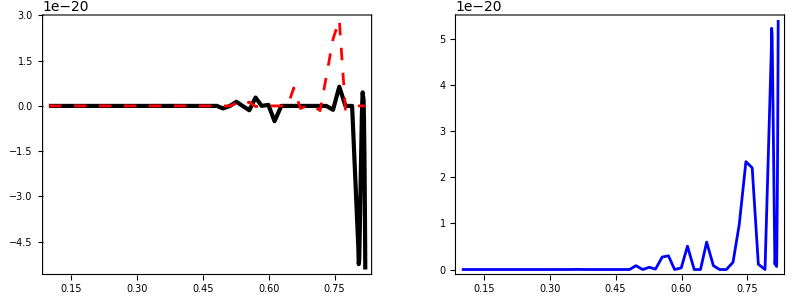

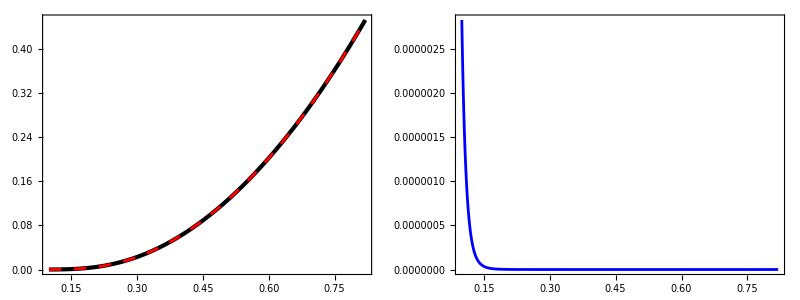

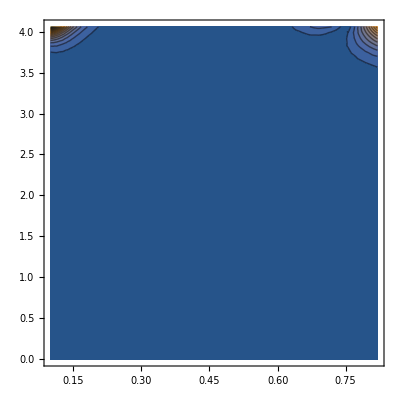

```mathematica
m = 0.938*GeVinversefm;
dof = 2.0;
θ=1.0;
N10Integrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*(pbar)^2*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N10GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*pbar*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N10=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N10Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N10GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10=Interpolation[N10];
N10Gauss=Interpolation[N10Gauss];
GraphicsGrid[{{Plot[{N10[T,μBmin],N10Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmin]-N10Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N10[T,μBmax],N10Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmax]-N10Gauss[T,μBmax])/N10Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Lambda

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

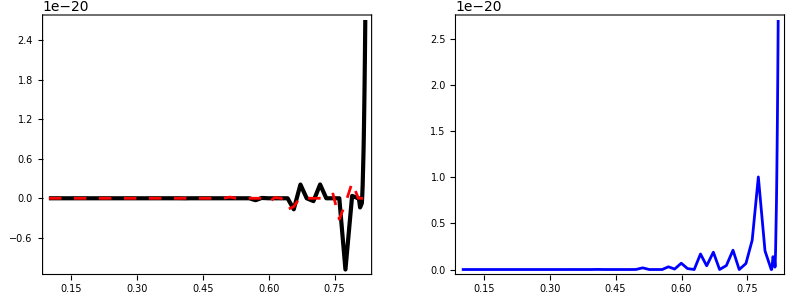

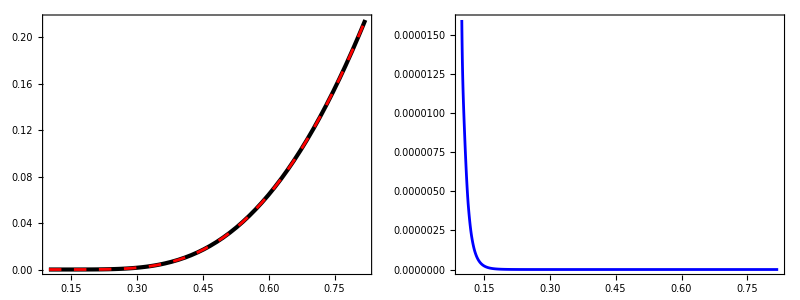

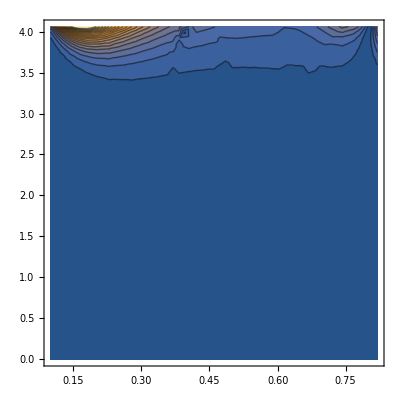

```mathematica
m = 1.11568*GeVinversefm;
dof = 2.0;
θ=1.0;
N10Integrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*(pbar)^2*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N10GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*pbar*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N10=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N10Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N10GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10=Interpolation[N10];
N10Gauss=Interpolation[N10Gauss];

GraphicsGrid[{{Plot[{N10[T,μBmin],N10Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmin]-N10Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N10[T,μBmax],N10Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmax]-N10Gauss[T,μBmax])/N10Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

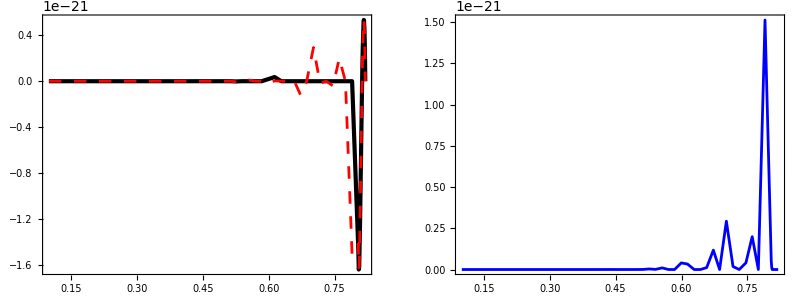

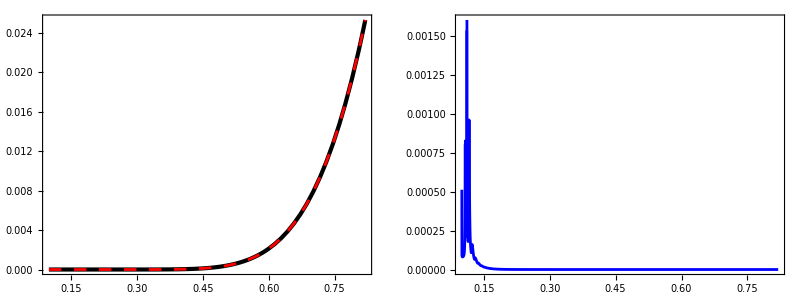

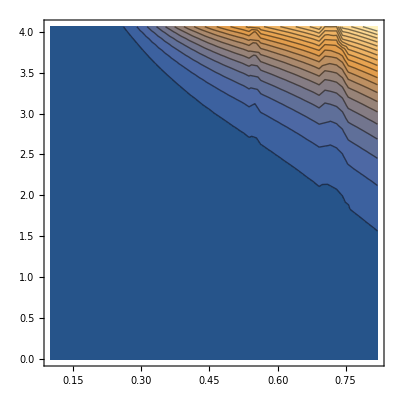

```mathematica
m = 1.67243*GeVinversefm;
dof = 4.0;
θ=1.0;
N10Integrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*(pbar)^2*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N10GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*pbar*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N10=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N10Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N10GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10=Interpolation[N10];
N10Gauss=Interpolation[N10Gauss];
GraphicsGrid[{{Plot[{N10[T,μBmin],N10Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmin]-N10Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N10[T,μBmax],N10Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmax]-N10Gauss[T,μBmax])/N10Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega2250

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

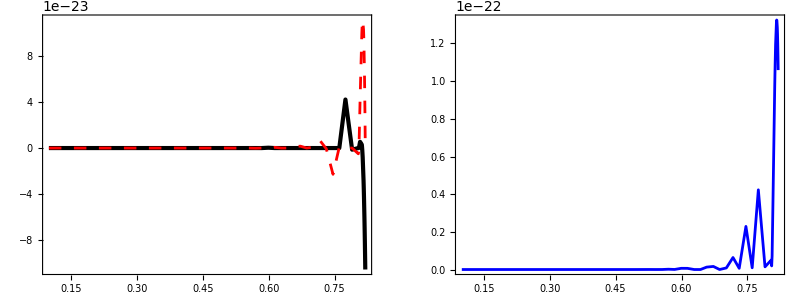

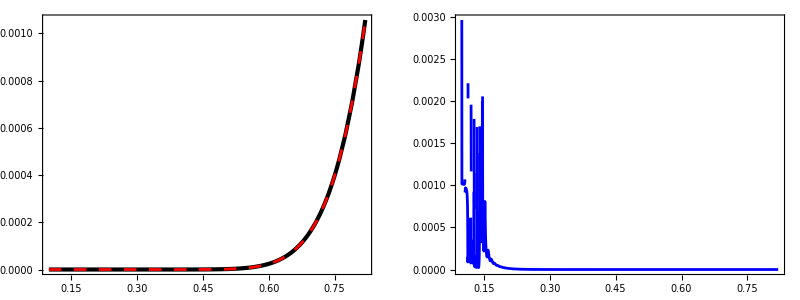

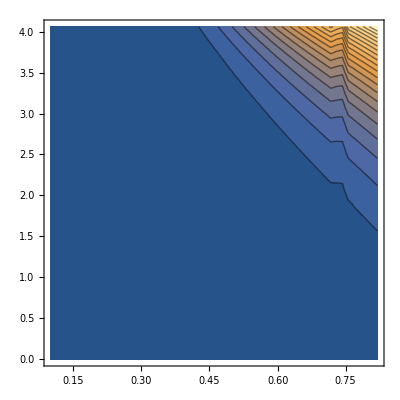

```mathematica
m = 2.25200*GeVinversefm;
dof = 4.0;
θ=1.0;
N10Integrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*(pbar)^2*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
N10GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^3)/(2.0*Pi^2)*pbar*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)-Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

N10=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[N10Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*N10GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
N10=Interpolation[N10];
N10Gauss=Interpolation[N10Gauss];
GraphicsGrid[{{Plot[{N10[T,μBmin],N10Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmin]-N10Gauss[T,μBmin])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{N10[T,μBmax],N10Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(N10[T,μBmax]-N10Gauss[T,μBmax])/N10Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(N10[T,μB]-N10Gauss[T,μB])]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```